```mathematica
ℏ=4.135667696*10^(-15); (*eV s*)
c=3*10^8
ϵ0=8.854187817*10^(-12)
```

300000000

8.85419×10^-12

### Coefientes de Mie

```mathematica
ψn[n_,ρ_]:= ρ*SphericalBesselJ[n,ρ]
```

```mathematica
ξn[n_,ρ_]:=ρ*SphericalHankelH1[n,ρ]
```

```mathematica
dψn[n_,ρ_]:=SphericalBesselJ[n-1,ρ]-(n+1)/ρ SphericalBesselJ[n,ρ]
dξn[n_,ρ_]:=0.5*(SphericalHankelH1[n-1,ρ]-(SphericalHankelH1[n,ρ]+ρ SphericalHankelH1[n+1,ρ])/ρ)
```

```mathematica
mieCoefAn[np_,nm_,a_,λ_,n_]:=Module[{m,x,an},
						m=np/nm;
						x=(2 Pi nm a)/λ;							
						an=((m ψn[n,m x] dψn[n,x])-(ψn[n,x] dψn[n,m x]))/((m ψn[n,m x] dξn[n,x])-(ξn[n,x] dψn[n,m x])); 
						an]
```

```mathematica
mieCoefBn[np_,nm_,a_,λ_,n_]:=Module[{m,x,bn},
						m=np/nm;
						x=(2 Pi nm a)/λ;							
						bn=((ψn[n,m x] dψn[n,x])-(m ψn[n,x] dψn[n,m x]))/((ψn[n,m x] dξn[n,x])-(m ξn[n,x] dψn[n,m x]));
						bn]
```

### Secciones transversales sin Drude

```mathematica
mieCsca[np_,nm_,a_,λ_,nmax_]:=Module[{k,Csca},
								k=2 Pi nm/λ;
				Csca =(2 Pi)/k^2 Sum[(2 n +1)(Norm[mieCoefAn[np,nm,a,λ,n]^2+Norm[mieCoefBn[np,nm,a,λ,n]]]^2),{n,1,nmax}]]
```

```mathematica
mieCext[np_,nm_,a_,λ_,nmax_]:=Module[{k,Cext},
k=2 Pi nm/λ;
Cext =(2 Pi)/k^2 Sum[(2 n +1)Re[(mieCoefAn[np,nm,a,λ,n]+mieCoefBn[np,nm,a,λ,n])],{n,1,nmax}]]
```

```mathematica
Qsca[np_,nm_,a_,λ_,nmax_]:=1/(Pi* a^2) mieCsca[np,nm,a,λ,nmax]
```

```mathematica
Qext[np_,nm_,a_,λ_,nmax_]:=1/(Pi* a^2) mieCext[np,nm,a,λ,nmax]
```

```mathematica
Plot[{Qsca[1,1.33,30*10^(-9),λ,100],Qext[1,1.33,30*10^(-9),λ,100]},{λ,0,100*10^(-9)},PlotRange->Full,PlotLabels->"Expressions"]
```

-Graphics-

## Modelo de Drude

```mathematica
ϵ[λ_,λp_,γ_]:=1-((2 Pi c/λp)^2/((2 Pi c/λ)((2 Pi c/λ)+ ⅈ  γ)))(*unidades en SI*)
```

### Coefientes de Mie

```mathematica
drudemieCoefAn[nm_,a_,λ_,λp_,γ_,n_]:=Module[{ϵ,np,m,x,an},
						ϵ=1-((2 Pi c/λp)^2/((2 Pi c/λ)((2 Pi c/λ)+ ⅈ  γ)));
						np=Sqrt[ϵ];
						m=np/nm;
						x=(2 Pi nm a)/λ;							
						an=((m ψn[n,m x] dψn[n,x])-(ψn[n,x] dψn[n,m x]))/((m ψn[n,m x] dξn[n,x])-(ξn[n,x] dψn[n,m x])); 
						an]
```

```mathematica
(*************************************************************************************************************)
(*PRUEBAS*)
```

```mathematica
ϵ[100*10^(-9),150*10^(-9),0.0003/ℏ]
```

0.555556+1.71038×10^-6 ⅈ

```mathematica
Sqrt[0.5555555555621376+1.710377512449371*^-6 ⅈ]
```

0.745356+1.14736×10^-6 ⅈ

```mathematica
mieCoefAn[0.7453559925052284+1.1473561154989797*^-6 ⅈ,1.33,30*10^(-9),200*10^(-9),10]
```

1.41592×10^-23+8.18951×10^-18 ⅈ

```mathematica
drudemieCoefAn[1.33,30*10^(-9),200*10^(-9),150*10^(-9),0.0003/ℏ,10]
```

-6.51951×10^-18+9.77201×10^-18 ⅈ

```mathematica
(********************************************************************************************************)
```

```mathematica
drudemieCoefBn[nm_,a_,λ_,λp_,γ_,n_]:=Module[{ϵ,np,m,x,bn},
						ϵ=1-((2 Pi c/λp)^2/((2 Pi c/λ)((2 Pi c/λ)+ ⅈ  γ)));
						np=Sqrt[ϵ];
						m=np/nm;
						x=(2 Pi nm a)/λ;								
						bn=((ψn[n,m x] dψn[n,x])-(m ψn[n,x] dψn[n,m x]))/((ψn[n,m x] dξn[n,x])-(m ξn[n,x] dψn[n,m x]));
						bn]
```

```mathematica
(*************************************************************************************************************)
(*PRUEBAS*)
```

```mathematica
mieCoefBn[7.757543221557538*^-6+0.8819171036626078 ⅈ,1.33,30*10^(-9),200*10^(-9),10]
```

1.07306×10^-17+4.09606×10^-18 ⅈ

```mathematica
drudemieCoefBn[1.33,30*10^(-9),200*10^(-9),150*10^(-9),0.0003/ℏ,10]
```

1.07306×10^-17+4.09606×10^-18 ⅈ

```mathematica
(*************************************************************************************************************)
```

### Secciones transversales con Drude

```mathematica
drudeMieCsca[nm_,a_,λ_,λp_,γ_,nmax_]:=Module[{ϵ,np,m,k,Csca},
											ϵ=1-((2 Pi c/λp)^2/((2 Pi c/λ)((2 Pi c/λ)+ ⅈ  γ)));
											np=Sqrt[ϵ];
											m=np/nm;
											k=2 Pi nm/λ;
		Csca =(2 Pi)/k^2 Sum[(2 n +1)(Norm[drudemieCoefAn[nm,a,λ,λp,γ,n]]^2+Norm[drudemieCoefBn[nm,a,λ,λp,γ,n]]^2),{n,1,nmax}]]
```

```mathematica
(*************************************************************************************************************)
(*PRUEBAS*)
```

```mathematica
mieCsca[7.757543221557538*^-6+0.8819171036626078 ⅈ,1.33,30*10^(-9),200*10^(-9),10]
```

1.55168×10^-16

```mathematica
drudeMieCsca[1.33,30*10^(-9),200*10^(-9),150*10^(-9),0.0003/ℏ,10]
```

2.36573×10^-15

```mathematica
(*PRUEBAS*)
```

```mathematica
drudeMieCsca[1.33,30*10^(-9),10*10^(-6),2 Pi c/(4.3/ℏ),(0.15/ℏ),50]
```

General::munfl: (6.36718×10^-161)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (6.04618×10^-161)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.27812×10^-167)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-2.22064×10^-23-4.42368×10^-24 ⅈ

```mathematica
drudeMieCext[nm_,a_,λ_,λp_,γ_,nmax_]:=Module[{ϵ,np,m,k,Cext},
											ϵ=1-((2 Pi c/λp)^2/((2 Pi c/λ)((2 Pi c/λ)+ ⅈ  γ)));
											np=Sqrt[ϵ];
											m=np/nm;
											k=2 Pi np/λ;
Cext =(2 Pi)/k^2 Sum[(2 n +1)Re[(drudemieCoefAn[nm,a,λ,λp,γ,n]+drudemieCoefBn[nm,a,λ,λp,γ,n])],{n,1,nmax}]]
```

```mathematica
drudeQsca[nm_,a_,λ_,λp_,γ_,nmax_]:=1/(Pi* a^2) drudeMieCsca[nm,a,λ,λp,γ,nmax]
```

```mathematica
drudeQext[nm_,a_,λ_,λp_,γ_,nmax_]:=1/(Pi* a^2) drudeMieCext[nm,a,λ,λp,γ,nmax]
```

```mathematica
drudeQsca[1,60*10^(-9),100*10^(9),2 Pi c/(13.142/ℏ),0.197/ℏ,1]
```

-1.40348×10^-105-5.98678×10^-90 ⅈ

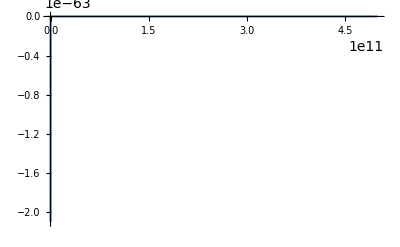

```mathematica
Plot[{Re[drudeQsca[1,60*10^(-9),λ,2 Pi c/(13.142/ℏ),0.197/ℏ,2]]},{λ,0,500*10^(9)},PlotRange->Full]
```

```mathematica
(3+4I)^2
```

-7+24 ⅈ

```mathematica
(3+4I)*(3-4I)
```

25